### Start choosing the example:

```mathematica
t=3;
beta=0;
A=0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U1->15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 1.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.009266,Null}

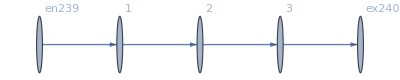

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j241→80.,j242→80.,j243→80.,j244→80.,j245→0.,j246→0.,j247→0.,j248→0.,jt249→0.,jt250→80.,jt251→80.,jt252→0.,jt253→80.,jt254→0.,u255→175.,u256→95.,u257→15.,u258→175.,u259→95.,u260→15.,u261→15.,u262→175.|>

#### Non-linear case

```mathematica
alpha=0;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.14725×10^-17

<|j241→80,j242→80,j243→80,j244→80,j245→0.,j246→0.,j247→0.,j248→0.,jt249→0.,jt250→80,jt251→80,jt252→0.,jt253→80,jt254→0.,u255→20.1639,u256→17.582,u257→15.,u258→20.1639,u259→17.582,u260→15.,u261→15.,u262→20.1639|>

```mathematica
alpha=0.1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 4.6236×10^-17

<|j241→80,j242→80,j243→80,j244→80,j245→0.,j246→0.,j247→0.,j248→0.,jt249→0.,jt250→80,jt251→80,jt252→0.,jt253→80,jt254→0.,u255→21.3227,u256→18.1613,u257→15.,u258→21.3227,u259→18.1613,u260→15.,u261→15.,u262→21.3227|>

```mathematica
alpha=0.3;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 7.10769×10^-17

<|j241→80,j242→80,j243→80,j244→80,j245→0.,j246→0.,j247→0.,j248→0.,jt249→0.,jt250→80,jt251→80,jt252→0.,jt253→80,jt254→0.,u255→25.0478,u256→20.0239,u257→15.,u258→25.0478,u259→20.0239,u260→15.,u261→15.,u262→25.0478|>

```mathematica
alpha=1;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.20583×10^-13,ComplexInfinity]

<|j241→80,j242→80,j243→80,j244→80,j245→0.,j246→0.,j247→0.,j248→0.,jt249→0.,jt250→80,jt251→80,jt252→0.,jt253→80,jt254→0.,u255→175.,u256→95.,u257→15.,u258→175.,u259→95.,u260→15.,u261→15.,u262→175.|>

```mathematica
alpha=1.2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j241→80,j242→80,j243→80,j244→80,j245→0.,j246→0.,j247→0.,j248→0.,jt249→0.,jt250→80,jt251→80,jt252→0.,jt253→80,jt254→0.,u255→742.811,u256→378.906,u257→15.,u258→742.811,u259→378.906,u260→15.,u261→15.,u262→742.811|>

```mathematica
alpha=1.6;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j241→80,j242→80,j243→80,j244→80,j245→0.,j246→0.,j247→0.,j248→0.,jt249→0.,jt250→80,jt251→80,jt252→0.,jt253→80,jt254→0.,u255→580101.,u256→290058.,u257→15.,u258→580101.,u259→290058.,u260→15.,u261→15.,u262→580101.|>

```mathematica
alpha=1.7;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j241→80,j242→80,j243→80,j244→80,j245→0.,j246→0.,j247→0.,j248→0.,jt249→0.,jt250→80,jt251→80,jt252→0.,jt253→80,jt254→0.,u255→3.119×10^7,u256→1.5595×10^7,u257→15.,u258→3.119×10^7,u259→1.5595×10^7,u260→15.,u261→15.,u262→3.119×10^7|>

```mathematica
alpha=1.8;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j241→80,j242→80,j243→80,j244→80,j245→0.,j246→0.,j247→0.,j248→0.,jt249→0.,jt250→80,jt251→80,jt252→0.,jt253→80,jt254→0.,u255→4.81052×10^10,u256→2.40526×10^10,u257→15.,u258→4.81052×10^10,u259→2.40526×10^10,u260→15.,u261→15.,u262→4.81052×10^10|>

```mathematica
alpha=1.9;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j241→80,j242→80,j243→80,j244→80,j245→0.,j246→0.,j247→0.,j248→0.,jt249→0.,jt250→80,jt251→80,jt252→0.,jt253→80,jt254→0.,u255→1.12074×10^19,u256→5.6037×10^18,u257→15.,u258→1.12074×10^19,u259→5.6037×10^18,u260→15.,u261→15.,u262→1.12074×10^19|>

```mathematica
alpha=2;
Parameters["alpha"]=alpha;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j241→80,j242→80,j243→80,j244→80,j245→0.,j246→0.,j247→0.,j248→0.,jt249→0.,jt250→80,jt251→80,jt252→0.,jt253→80,jt254→0.,u255→4.4098×10^106,u256→2.2049×10^106,u257→15.,u258→4.4098×10^106,u259→2.2049×10^106,u260→15.,u261→15.,u262→4.4098×10^106|>